```mathematica
ClearAll["Global`*"]
```

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../../../Tools/Mathematica/triangulation.nb"]
```

```mathematica
iDir=NotebookDirectory[];
SetDirectory@iDir;
```

## Расчётная область

### Входные параметры для определения геометрии

```mathematica
a=.06; (* 6 сантиметров *)
b=.1;
c=.06;
d=.04;
f=.01;
k=.02;
r=.002;
s=.02; (* ширина воздушной прослойки *)
```

```mathematica
-Graphics--Graphics-
```

### Построение области

#### Границы подобластей

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
(* основной прямоугольник / воздух *)
air={{-s,0},{-s,a+s},{b+s,a+s},{b+s,0}};
default={{-.02,0},{-.02,a+.02},{b+.02,a+.02},{b+.02,0}};
(* магнит *)
magnet={
{0,0},{0,a},{b,a},{b,0},
{(b-c)/2,0},{(b-c)/2,d},{(b-c)/2+(c-k)/2,d},{(b-c)/2+(c-k)/2,r},{(b-c)/2+(c-k)/2+k,r},{(b-c)/2+(c-k)/2+k,d},{c+(b-c)/2,d},{c+(b-c)/2,0}
};
field=Flatten[Table[{x,y},{x,.03,.07,(.04)/4},{y,{0,r}}],1];
(* левая обмотка *)
w=(c-k)/4-f/2;
left={{(b-c)/2+w,d-f-w},{(b-c)/2+w,d-w},{(b-c)/2+f+w,d-w},{(b-c)/2+f+w,d-f-w}};
right=(#+{2w+f+k,0})&/@left;
```

```mathematica
boundaryMesh=ToBoundaryMesh["Coordinates"-> Join[default,air,magnet,left,right],"BoundaryElements"->LineElement/@{
{{1,2},{2,3},{3,4},{4,1}},
{{5,6},{6,7},{7,8},{8,5}},
{{9,10},{10,11},{11,12},{12,20},{20,19},{19,18},{18,17},{17,16},{16,15},{15,14},{14,13},{13,9}},{{21,22},{22,23},{23,24},{24,21}},
{{25,26},{26,27},{27,28},{28,25}}
}];
boundaryMesh["Wireframe"]
```

#### Символические подобласти

```mathematica
Needs["Notation`"]
```

```mathematica
Symbolize[Subscript[Ω, _]]
Symbolize[Subscript[pΩ, _]]
```

```mathematica
opacity=.5;
```

```mathematica
Ω=Rectangle[air[[1]],air[[3]]];
pΩ=RegionPlot[Ω,PlotStyle->Opacity@0.,BoundaryStyle->Black,AspectRatio->Automatic];
```

```mathematica
Subscript[Ω, default]=Rectangle[{-.02,0},{b+.02,a+.02}];
Subscript[pΩ, default]=RegionPlot[Subscript[Ω, default],PlotStyle->Opacity@0.,BoundaryStyle->Black,AspectRatio->Automatic];
```

```mathematica
Subscript[Ω, left]=Rectangle[{.025,.025},{.035,.035}];
Subscript[pΩ, left]=RegionPlot[Subscript[Ω, left],PlotStyle->Directive[Red,Opacity@opacity],BoundaryStyle->Black,AspectRatio->Automatic];
```

```mathematica
Subscript[Ω, right]=Rectangle[{.065,0.025},{.075,.035}];
Subscript[pΩ, right]=RegionPlot[Subscript[Ω, right],PlotStyle->Directive[Blue,Opacity@opacity],BoundaryStyle->Black,AspectRatio->Automatic];
```

```mathematica
Subscript[Ω, magnet]=RegionUnion[
Rectangle[{0.,0.},{.02,.06}],
Rectangle[{.04,.002},{.06,.04}],
Rectangle[{.08,0.},{.1,.06}],
Rectangle[{0.,.04},{.1,.06}]
];
Subscript[pΩ, magnet]=RegionPlot[Subscript[Ω, magnet],PlotStyle->Directive[Gray,Opacity@opacity],BoundaryStyle->Black,AspectRatio->Automatic];
```

```mathematica
Subscript[Ω, field]=Rectangle[{4.5/100,0},{5.5/100,2/1000}];
Subscript[pΩ, field]=RegionPlot[Subscript[Ω, field],PlotStyle->Directive[Yellow,Opacity@opacity],BoundaryStyle->Black,AspectRatio->Automatic];
```

#### Сетка (с измельчением близ разрывов)

```mathematica
elementMeshGood=ToElementMesh[boundaryMesh,"MeshOrder"->1,"RegionMarker"->{{{.05,.05},1,(.0001)/4}},"MaxCellMeasure"->∞];
frameGood=elementMeshGood["Wireframe"];
```

```mathematica
Show[pΩ,Subscript[pΩ, default],Subscript[pΩ, left],Subscript[pΩ, right],Subscript[pΩ, magnet],Subscript[pΩ, field],frameGood,ImageSize->400]
```

```mathematica
(* export CATS’ PDEs mesh *)
meshGood=create𝒯fromElementMesh@elementMeshGood;
export[meshGood,"mesh_good",<|"format"->"NT"|>]
```

#### Сетка (грубая)

```mathematica
elementMeshCoarse=ToElementMesh[boundaryMesh,"MeshOrder"->1,"MaxCellMeasure"->∞];
frameCoarse=elementMeshCoarse["Wireframe"];
```

```mathematica
Show[pΩ,Subscript[pΩ, default],Subscript[pΩ, left],Subscript[pΩ, right],Subscript[pΩ, magnet],Subscript[pΩ, field],frameCoarse,ImageSize->400]
```

```mathematica
(* export CATS’ PDEs mesh *)
meshCoarse=create𝒯fromElementMesh@elementMeshCoarse;
export[meshCoarse,"mesh_coarse",<|"format"->"NT"|>]
```

#### Сетка (неконформная к разрывам)

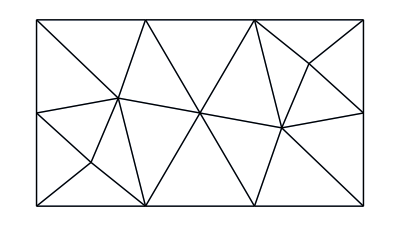

```mathematica
meshNonconform=create𝒯fromRegion[Rectangle[{-s,0},{b+s,a+s}],.001];
highlight[meshNonconform,{},0]
```

```mathematica
export[meshNonconform,"mesh_nonconform",<|"format"->"NT"|>]
```

mesh_nonconform.nt

## Интерполянт (μ̂)_iron(||B⃗||) для нелинейной задачи

```mathematica
Symbolize[Subscript[μ, _]]
```

```mathematica
Symbolize[Subscript[μ̄, _]]
```

```mathematica
Symbolize[Subscript[B, _]]
```

```mathematica
data=#[[{2,1}]]&/@Import@"mu.001";
```

```mathematica
BnValues=First/@data;
muValues=Last/@data;
```

### Интерполянт

```mathematica
Subscript[μ̂, ironInt]=Interpolation[data,InterpolationOrder->1];
```

### Экстраполянт

```mathematica
Clear@Subscript[B, max]
```

```mathematica
Clear@Subscript[μ, n]
```

```mathematica
Subscript[μ̂, ironExt][B_]=Quiet@Solve[1/m==Subscript[B, max]/B(1/Subscript[μ, n]-1)+1,m][[1,1,2]]
```

```mathematica
Limit[Subscript[μ̂, ironExt][B],B->∞]
Limit[D[Subscript[μ̂, ironExt][B],B],B->Infinity]
```

### Итоговая зависимость

```mathematica
{Subscript[B, min],Subscript[B, max]}={First@BnValues,Last@BnValues};
{Subscript[μ, 0],Subscript[μ, n]}={First@muValues,Last@muValues};
```

```mathematica
Show[
Plot[Subscript[μ, 0],{B,0,Subscript[B, min]},PlotRange->{{Subscript[B, max]-2,Subscript[B, max]+2},{.5,3}},PlotStyle->{Red,Thick}],
Plot[Subscript[μ̂, ironInt][B],{B,Subscript[B, min],Subscript[B, max]}],
Plot[Subscript[μ̂, ironExt][B],{B,Subscript[B, max],Subscript[B, max]+5},PlotStyle->{Red,Thick}],
ImageSize->400
]
```

```mathematica
Export["Bn_values.dat",Prepend[BnValues,Length@BnValues]];
Export["mu_values.dat",muValues];
```